```mathematica
Quit
```

## MC Values (from Jess)

```mathematica
SetDirectory["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Mathematica codes/MC Results"];
```

```mathematica
mcmcFiles=<|"Model 1"->"mcmc_parameter_summary_model_1_20000steps.csv","Model 2"->"mcmc_parameter_summary_model_2_20000steps.csv","Model 3"->"mcmc_parameter_summary_model_3_50000steps.csv"|>;
```

```mathematica
paramColumnMap=<|"H0_mean"->"H0","q0_mean"->"q0","j0_mean"->"j0","Om0_mean"->"Om0","eps_mean"->"eps","wDE0_mean"->"wDE0","wDE0p_mean"->"wDE0p"|>;
```

```mathematica
(*Build the nested association for a single model's CSV file*)
BuildModelParams[file_String]:=Module[{data,header,rows},data=Import[file,"Data"];
header=First[data];
rows=Rest[data];
Association[Map[Function[row,Module[{assocFull,datasetName},assocFull=AssociationThread[header->row];
datasetName=assocFull["dataset"];
datasetName->Association[KeyValueMap[Function[{oldKey,newKey},newKey->assocFull[oldKey]],paramColumnMap]]]],rows]]];
```

```mathematica
(*Master nested association:allParams["Model 1"]["DESI"]-><|"H0"->...,...|>*)
allParams=Association[KeyValueMap[Function[{modelName,file},modelName->BuildModelParams[file]],mcmcFiles]];
```

```mathematica
(* ============================================================*)
(*Convenience accessors*)
(* ============================================================*)

(*List available models*)
AvailableModels[]=Keys[allParams];
AvailableDatasets[model_String]:=Keys[allParams[model]];
```

```mathematica
AvailableModels[]
```

{Model 1,Model 2,Model 3}

```mathematica
AvailableDatasets["Model 1"]
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

```mathematica
(*(*Main getter:GetParams["Model 1","DESI"]->Association of params*)
GetParams[model_String,dataset_String]:=Module[{},If[!KeyExistsQ[allParams,model],Message[GetParams::nomodel,model,AvailableModels[]];
Return[$Failed]];
If[!KeyExistsQ[allParams[model],dataset],Message[GetParams::nodataset,dataset,model,AvailableDatasets[model]];
Return[$Failed]];
allParams[model][dataset]];

GetParams::nomodel="Model `1` not found. Available models: `2`";
GetParams::nodataset="Dataset `1` not found for `2`. Available datasets: `3`";*)
```

```mathematica
(*Map model name->jModel function*)
jModelMap=<|"Model 1"->j1,"Model 2"->j2,"Model 3"->j3|>;
```

```mathematica
(*Main getter:GetParams["Model 1","DESI"]->Association of params,including "j"*)
GetParams[model_String,dataset_String]:=Module[{baseParams},If[!KeyExistsQ[allParams,model],Message[GetParams::nomodel,model,AvailableModels[]];
Return[$Failed]];
If[!KeyExistsQ[allParams[model],dataset],Message[GetParams::nodataset,dataset,model,AvailableDatasets[model]];
Return[$Failed]];
baseParams=allParams[model][dataset];
Append[baseParams,"j"->jModelMap[model]]];
```

### Model 1:

#### Desi Values

```mathematica
params1a=GetParams["Model 1","DESI"];
params1a["q0"]
params1a["Om0"]
params1a["eps"]
params1a["H0"]
```

-0.517033

0.498537

-0.0258394

68.2919

```mathematica
(*H01a=68.29192059313633;
q01a=-0.5170327771473278;
j01a=0.9625363652579005;
Ωm01a=0.4985365526609583;
ϵ1a=-0.025839351696166715;
wDE01a=-1.3514167286778105;*)
```

```mathematica
params10a=GetParams["Model 1","Planck + Union3 + Pantheon+ + DESY5"];
params10a["q0"]
params10a["Om0"]
params10a["eps"]
params10a["H0"]
```

-0.516172

0.31252

0.00132349

67.7409

### Model 2:

#### Desi Values

```mathematica
params2a=GetParams["Model 2","DESI"];
params2a["q0"]
params2a["Om0"]
params2a["eps"]
params2a["H0"]
```

-0.49883

0.491401

-0.100239

68.5342

```mathematica
H02a=68.53416748702578;
q02a=-0.49882983918505364;
j02a=0.8997606059127958;
Ωm02a=0.4914005086938241;
ϵ2a=-0.025839351696166715;
wDE02a=-1.3078293508597978;
```

### Model 3:

#### Desi Values

```mathematica
H03a=68.05462677945144;
q03a=-0.48266330038260274;
j03a=0.8033876955633561;
Ωm03a=0.5039105165387399;
ϵ3a=0.06671817784473298;
wDE03a=-1.3283914786225075;
```

## Equations

```mathematica
zPlot=10;
zinitial=100;
```

#### Defining the system of equations

```mathematica
dx= (1+z)x'[z]-(x[z]^2-x[z](2+q[z])-2-2q[z]+3Ω[z])==0;
dΩ=(1+z)Ω'[z]-Ω[z](x[z]+1-2q[z])==0;
dq=(1+z)q'[z]- (j[z]-q[z]-2 q[z]^2)==0;
dj= (1+z)j'[z]- (-s[z]-j[z](2+3q[z]))==0;
ds=(1+z)s'[z]- (-l[z]-s[z](3+4q[z]))==0;
dEh=(1+z)Eh'[z]- Eh[z](1+q[z])==0;
dH=(1+z)H'[z]- H[z](1+q[z])==0;
```

Autonomous system of equations
N=-ln(1+z) -> (1+z)d/dz = -d/dN

```mathematica
dxn= x'[n]+(x[n]^2-x[n](2+q[n])-2-2q[n]+3Ω[n])==0;
dΩn=Ω'[n]+Ω[n](x[n]+1-2q[n])==0;
dqn=q'[n]+ (j[n]-q[n]-2 q[n]^2)==0;
djn= j'[n]+ (-s[n]-j[n](2+3q[n]))==0;
dsn=s'[n]+ (-l[n]-s[n](3+4q[n]))==0;
dEhn=Eh'[n]+ Eh[n](1+q[n])==0;
dHn=H'[n]+ H[n](1+q[n])==0;
```

```mathematica
Fx[x_,Ω_,q_]:=-(x^2-x (2+q)-2-2 q+3 Ω);
FΩ[x_,Ω_,q_]:=-Ω (x+1-2 q);
Fq[q_,j_]:=-(j-q-2 q^2);
```

#### Models of j

```mathematica
j0[z_]=1;
j1[z_]=1+3ϵ(1+q[z]);
j2[z_]=1+ϵ;
j3[z_]=1+3ϵ(q[z]-1/2);
```

## Phase Space Analysis:

## Determining stability of fixed points

#### General fixed points for each model and specified dataset

```mathematica
FixedPointsStability[model_String,dataset_String]:=
Module[{params,epsVal,jExpr,jAlg,fps,Jac,classify,stabilityGrid},
params=GetParams[model,dataset];
epsVal=params["eps"];
jExpr=params["j"][n];

Block[{ϵ},ϵ=epsVal;
jAlg=jExpr/. q[n]->q;(*turn into algebraic expression in q*)
fps=NSolve[{Fx[x,Ω,q]==0,FΩ[x,Ω,q]==0,Fq[q,jAlg]==0},{x,Ω,q},Reals];

Jac[x_,Ω_,q_]=D[{Fx[x,Ω,q],FΩ[x,Ω,q],Fq[q,jAlg]},{{x,Ω,q}}];

classify[pt_]:=Module[{vals,eig,type},vals={x,Ω,q}/. pt;
eig=Eigenvalues[Jac@@vals]//N;
type=Which[AllTrue[eig,Re[#]<0&],"Stable node/spiral",AllTrue[eig,Re[#]>0&],"Unstable",True,"Saddle"];
{vals,eig,type}];
stabilityGrid=Grid[Prepend[classify/@fps,{"(x*, Ω*, q*)","Eigenvalues","Type"}],Frame->All];];
<|"model"->model,"dataset"->dataset,"eps"->epsVal,"fixedPoints"->fps,"stabilityGrid"->stabilityGrid|>];
```

```mathematica
fixedPointResults=Association[Map[Function[model,model->Association[Map[#->FixedPointsStability[model,#]&,AvailableDatasets[model]]]],AvailableModels[]]];
```

```mathematica
fixedPointResults["Model 1"]["DESI"]["stabilityGrid"]
```

(x*, Ω*, q*) | Eigenvalues | Type
{-3.,-4.,-1.} | {4.,-3.,3.} | Saddle
{1.,0.,-1.} | {-4.,-3.,-1.} | Stable node/spiral
{0.,0.,-1.} | {-3.,-3.,1.} | Saddle
{3.33702,0.,0.461241} | {-4.21279,-3.41454,2.84496} | Saddle
{-0.0775181,0.908561,0.461241} | {3.41454,2.84496,-0.798259} | Saddle
{-0.875777,0.,0.461241} | {4.21279,2.84496,0.798259} | Unstable

### Matter dominated fixed points

#### Matter dominated fixed point selection modules

```mathematica
(* ============================================================*)
(*Extract the matter-dominated fixed point:the one closest to (x,Ω,q)=(0,1,1/2),the eps->0 EdS limit*)
(* ============================================================*)
ExtractMatterDominatedFP[fps_List]:=Module[{target,distances,bestIdx},
target={0,1,1/2};
distances=Map[Function[pt,Module[{vals},vals={x,Ω,q}/. pt;
Norm[N[vals]-N[target]]]],fps];
bestIdx=First[Ordering[distances,1]];
fps[[bestIdx]]];
```

```mathematica
MatterDominatedFP[model_String,dataset_String]:=
Module[{fpResult,fps,bestFP,vals,eig,eigvecs,type,Jac,jAlg,epsVal},
fpResult=FixedPointsStability[model,dataset];

fps=fpResult["fixedPoints"];
epsVal=fpResult["eps"];
bestFP=ExtractMatterDominatedFP[fps];
vals={x,Ω,q}/. bestFP;

Block[{ϵ},ϵ=epsVal;
jAlg=GetParams[model,dataset]["j"][n]/. q[n]->q;
Jac[xx_,OOmega_,qq_]=D[{Fx[xx,OOmega,qq],FΩ[xx,OOmega,qq],Fq[qq,jAlg]},{{xx,OOmega,qq}}];
{eig,eigvecs}=Eigensystem[Jac@@vals]//N;];
type=Which[AllTrue[eig,Re[#]<0&],"Stable node/spiral",AllTrue[eig,Re[#]>0&],"Unstable",True,"Saddle"];

<|"model"->model,"dataset"->dataset,"eps"->epsVal,"x"->vals[[1]],"Ω"->vals[[2]],"q"->vals[[3]],"eigenvalues"->eig,"eigenvectors"->eigvecs,"type"->type|>];
```

```mathematica
matterDominatedFPs=Association[Map[Function[model,model->Association[Map[#->MatterDominatedFP[model,#]&,AvailableDatasets[model]]]],AvailableModels[]]];
```

#### Model 1 results

```mathematica
Grid[Prepend[Table[
{
dataset,
{matterDominatedFPs["Model 1"][dataset]["x"],matterDominatedFPs["Model 1"][dataset]["Ω"],matterDominatedFPs["Model 1"][dataset]["q"]},
matterDominatedFPs["Model 1"][dataset]["eigenvalues"],
matterDominatedFPs["Model 1"][dataset]["type"]
},

{dataset,AvailableDatasets["Model 1"]}],{"Dataset","{x*,Ω*,q*}","Eigenvalues","Type"}],Frame->All]
```

Dataset | {x*,Ω*,q*} | Eigenvalues | Type
DESI | {-0.0775181,0.908561,0.461241} | {3.41454,2.84496,-0.798259} | Saddle
Union3 | {-0.1625,0.806015,0.41875} | {3.44554,2.675,-0.70179} | Saddle
Pantheon+ | {-0.180312,0.784218,0.409844} | {3.452,2.63938,-0.681533} | Saddle
DESY5 | {-0.128173,0.847727,0.435914} | {3.43305,2.74365,-0.740793} | Saddle
Union3 + Pantheon+ + DESY5 | {-0.187075,0.775913,0.406463} | {3.45445,2.62585,-0.673838} | Saddle
Planck | {0.0288443,1.03351,0.514422} | {3.37532,3.05769,-0.91859} | Saddle
Planck + Union3 | {0.0196617,1.02287,0.509831} | {3.37873,3.03932,-0.908219} | Saddle
Planck + Pantheon+ | {0.0128663,1.01498,0.506433} | {3.38124,3.02573,-0.900542} | Saddle
Planck + DESY5 | {0.0165391,1.01925,0.50827} | {3.37988,3.03308,-0.904691} | Saddle
Planck + Union3 + Pantheon+ + DESY5 | {0.00397048,1.00463,0.501985} | {3.38453,3.00794,-0.890489} | Saddle

#### Model 2 results

```mathematica
Grid[Prepend[Table[{dataset,{matterDominatedFPs["Model 2"][dataset]["x"],matterDominatedFPs["Model 2"][dataset]["Ω"],matterDominatedFPs["Model 2"][dataset]["q"]},matterDominatedFPs["Model 2"][dataset]["eigenvalues"],matterDominatedFPs["Model 2"][dataset]["type"]},{dataset,AvailableDatasets["Model 2"]}],{"Dataset","{x*,Ω*,q*}","Eigenvalues","Type"}],Frame->All]
```

Dataset | {x*,Ω*,q*} | Eigenvalues | Type
DESI | {-0.0683851,0.919438,0.465807} | {3.41119,2.86323,-0.808608} | Saddle
Union3 | {-0.171988,0.794417,0.414006} | {3.44898,2.65602,-0.691001} | Saddle
Pantheon+ | {-0.207,0.751359,0.3965} | {3.46166,2.586,-0.651156} | Saddle
DESY5 | {-0.144586,0.827833,0.427707} | {3.43903,2.71083,-0.722151} | Saddle
Union3 + Pantheon+ + DESY5 | {-0.223659,0.730728,0.388171} | {3.46767,2.55268,-0.632178} | Saddle
Planck | {0.0304847,1.03541,0.515242} | {3.37472,3.06097,-0.920443} | Saddle
Planck + Union3 | {0.0214876,1.02499,0.510744} | {3.37805,3.04298,-0.910281} | Saddle
Planck + Pantheon+ | {0.0146289,1.01703,0.507314} | {3.38059,3.02926,-0.902533} | Saddle
Planck + DESY5 | {0.0184722,1.02149,0.509236} | {3.37917,3.03694,-0.906875} | Saddle
Planck + Union3 + Pantheon+ + DESY5 | {0.00556607,1.00649,0.502783} | {3.38394,3.01113,-0.892292} | Saddle

#### Model 3 results

```mathematica
Grid[Prepend[Table[{dataset,{matterDominatedFPs["Model 3"][dataset]["x"],matterDominatedFPs["Model 3"][dataset]["Ω"],matterDominatedFPs["Model 3"][dataset]["q"]},matterDominatedFPs["Model 3"][dataset]["eigenvalues"],matterDominatedFPs["Model 3"][dataset]["type"]},{dataset,AvailableDatasets["Model 3"]}],{"Dataset","{x*,Ω*,q*}","Eigenvalues","Type"}],Frame->All]
```

Dataset | {x*,Ω*,q*} | Eigenvalues | Type
DESI | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Union3 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Pantheon+ | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
DESY5 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Union3 + Pantheon+ + DESY5 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Planck | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Planck + Union3 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Planck + Pantheon+ | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Planck + DESY5 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Planck + Union3 + Pantheon+ + DESY5 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle

## Background Solution

```mathematica
SetDirectory@NotebookDirectory[];
```

## Obtaining Background solutions q(z) and E(z)

### Obtaining q(z)

```mathematica
SolveForq[model_String,dataset_String]:=
Module[{params,odeQ,sol},
params=GetParams[model,dataset];
odeQ={dq/. j->params["j"]/. ϵ->params["eps"],q[0]==params["q0"]};
sol=NDSolve[odeQ,q,{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10];
q/. sol[[1]]];
```

```mathematica
qSolAllSets1=Association[Map[#->SolveForq["Model 1",#]&,AvailableDatasets["Model 1"]]];
qSolAllSets2=Association[Map[#->SolveForq["Model 2",#]&,AvailableDatasets["Model 2"]]];
qSolAllSets3=Association[Map[#->SolveForq["Model 3",#]&,AvailableDatasets["Model 3"]]];
```

```mathematica
qSolAllSets3["DESI"][0]
```

-0.482663

#### Model 1, All datasets

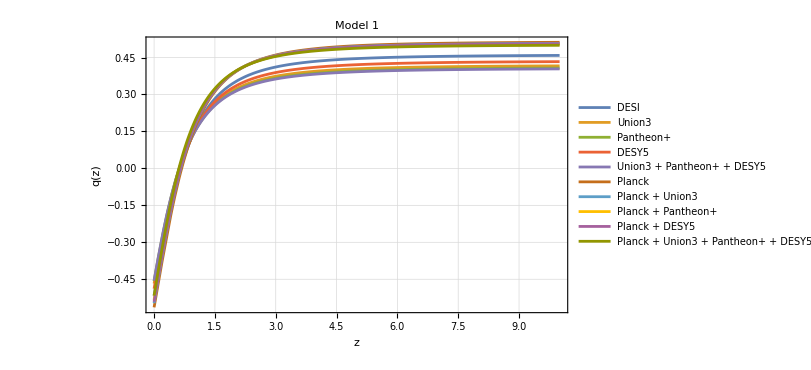

```mathematica
Plot[Evaluate[Table[qSolAllSets1[d][z],{d,Keys[qSolAllSets1]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[qSolAllSets1],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.55,0.25}],Frame->True,FrameLabel->{"z","q(z)"},PlotLabel->"Model 1",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

#### Model 2, All datasets

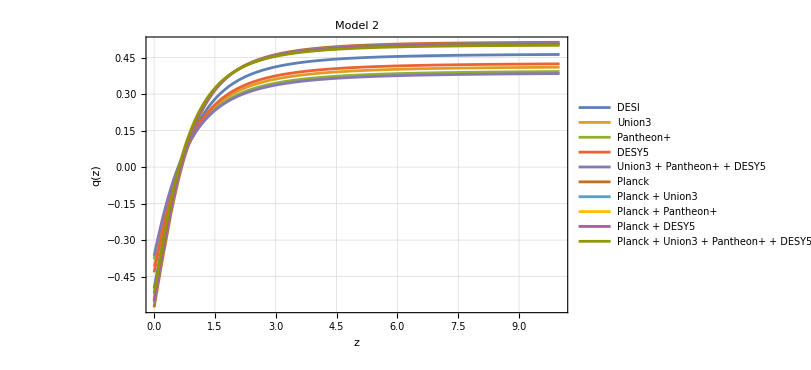

```mathematica
Plot[Evaluate[Table[qSolAllSets2[d][z],{d,Keys[qSolAllSets2]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[qSolAllSets2],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.55,0.25}],Frame->True,FrameLabel->{"z","q(z)"},PlotLabel->"Model 2",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

#### Model 3, All datasets

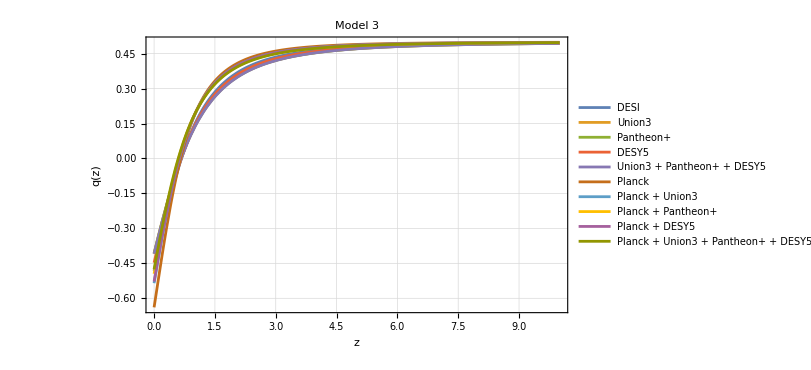

```mathematica
Plot[Evaluate[Table[qSolAllSets3[d][z],{d,Keys[qSolAllSets3]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[qSolAllSets3],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.55,0.25}],Frame->True,FrameLabel->{"z","q(z)"},PlotRange->All,PlotLabel->"Model 3",GridLines->Automatic,ImageSize->600]
```

#### Plotting for a specific dataset

```mathematica
AvailableDatasets["Model 1"]
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

```mathematica
DataSetPlot=AvailableDatasets["Model 1"][[1]]
```

DESI

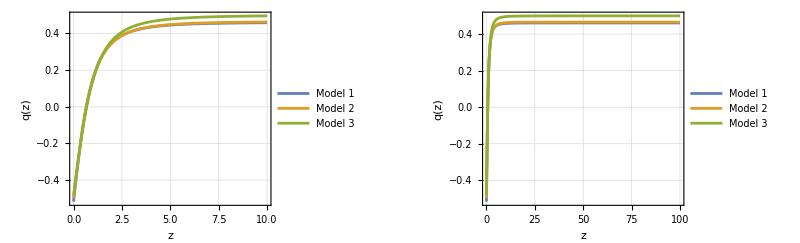

```mathematica
GraphicsRow[{
Plot[{qSolAllSets1[DataSetPlot][z],qSolAllSets2[DataSetPlot][z],qSolAllSets3[DataSetPlot][z]},{z,0,zPlot},FrameLabel->{"z","q(z)"},GridLines->Automatic,ImageSize->Full,Frame->True,PlotRange->All,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.25}]],
Plot[{qSolAllSets1[DataSetPlot][z],qSolAllSets2[DataSetPlot][z],qSolAllSets3[DataSetPlot][z]},{z,0,zinitial},FrameLabel->{"z","q(z)"},GridLines->Automatic,Frame->True,PlotRange->All,ImageSize->Full,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.25}]]},ImageSize->Full]
```

### Obtaining E(z)

```mathematica
SolveForEh[model_String,dataset_String]:=
Module[{params,qFn,odeEh,sol},
params=GetParams[model,dataset];
qFn=SolveForq[model,dataset];

odeEh={(dEh/. q->qFn)/. ϵ->params["eps"],Eh[0]==1};
sol=NDSolve[odeEh,Eh,{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10];
Eh/. sol[[1]]];
```

```mathematica
hSolAllSets1=Association[Map[#->SolveForEh["Model 1",#]&,AvailableDatasets["Model 1"]]];
hSolAllSets2=Association[Map[#->SolveForEh["Model 2",#]&,AvailableDatasets["Model 2"]]];
hSolAllSets3=Association[Map[#->SolveForEh["Model 3",#]&,AvailableDatasets["Model 3"]]];
```

#### Model 1, All datasets

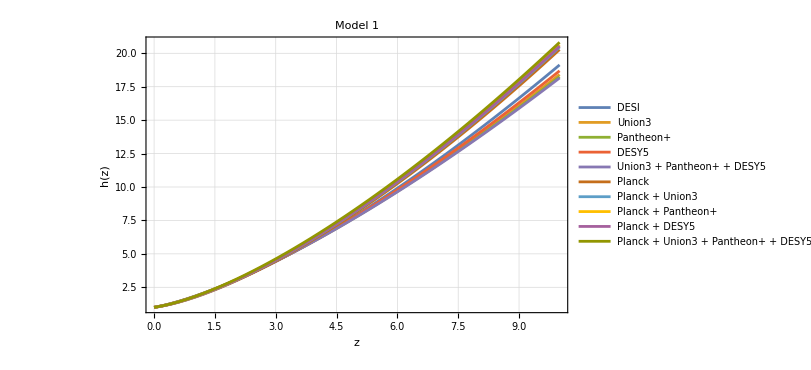

```mathematica
Plot[Evaluate[Table[hSolAllSets1[d][z],{d,Keys[hSolAllSets1]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[hSolAllSets1],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.45,0.8}],Frame->True,FrameLabel->{"z","h(z)"},PlotLabel->"Model 1",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

```mathematica
TableForm[Table[{d,hSolAllSets1[d][zinitial]},{d,Keys[hSolAllSets1]}],TableHeadings->{None,{"Dataset","h(zInitial)"}}]
```

Dataset | h(zInitial)
DESI | 487.972
Union3 | 427.448
Pantheon+ | 415.232
DESY5 | 450.691
Union3 + Pantheon+ + DESY5 | 410.135
Planck | 582.087
Planck + Union3 | 581.734
Planck + Pantheon+ | 581.603
Planck + DESY5 | 581.552
Planck + Union3 + Pantheon+ + DESY5 | 581.399

#### Model 2, All datasets

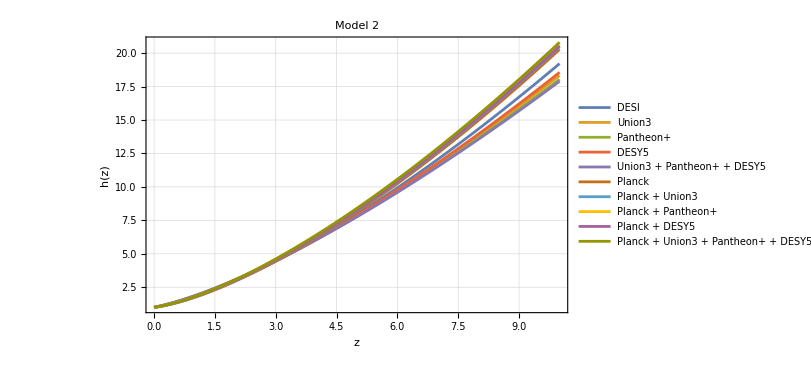

```mathematica
Plot[Evaluate[Table[hSolAllSets2[d][z],{d,Keys[hSolAllSets2]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[hSolAllSets1],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.45,0.8}],Frame->True,FrameLabel->{"z","h(z)"},PlotLabel->"Model 2",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

```mathematica
TableForm[Table[{d,hSolAllSets2[d][zinitial]},{d,Keys[hSolAllSets2]}],TableHeadings->{None,{"Dataset","h(zInitial)"}}]
```

Dataset | h(zInitial)
DESI | 495.091
Union3 | 420.89
Pantheon+ | 398.454
DESY5 | 439.402
Union3 + Pantheon+ + DESY5 | 387.995
Planck | 583.147
Planck + Union3 | 582.678
Planck + Pantheon+ | 582.296
Planck + DESY5 | 582.496
Planck + Union3 + Pantheon+ + DESY5 | 582.041

#### Model 3, All datasets

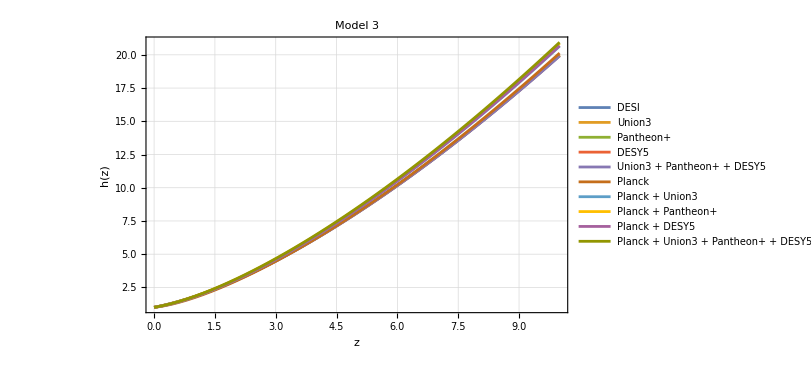

```mathematica
Plot[Evaluate[Table[hSolAllSets3[d][z],{d,Keys[hSolAllSets3]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[hSolAllSets1],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.45,0.8}],Frame->True,FrameLabel->{"z","h(z)"},PlotLabel->"Model 3",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

```mathematica
TableForm[Table[{d,hSolAllSets3[d][zinitial]},{d,Keys[hSolAllSets3]}],TableHeadings->{None,{"Dataset","h(zInitial)"}}]
```

Dataset | h(zInitial)
DESI | 554.159
Union3 | 555.
Pantheon+ | 554.161
DESY5 | 553.977
Union3 + Pantheon+ + DESY5 | 552.693
Planck | 559.824
Planck + Union3 | 574.249
Planck + Pantheon+ | 579.725
Planck + DESY5 | 575.118
Planck + Union3 + Pantheon+ + DESY5 | 582.131

#### Plotting for a specific dataset

```mathematica
AvailableDatasets["Model 1"]
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

```mathematica
DataSetPlot=AvailableDatasets["Model 1"][[1]]
```

DESI

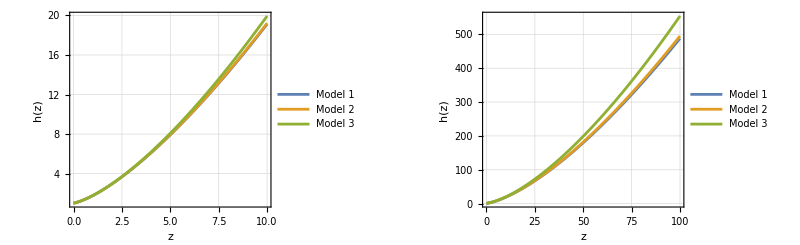

```mathematica
GraphicsRow[{
Plot[{hSolAllSets1[DataSetPlot][z],hSolAllSets2[DataSetPlot][z],hSolAllSets3[DataSetPlot][z]},{z,0,zPlot},FrameLabel->{"z","h(z)"},GridLines->Automatic,ImageSize->Full,Frame->True,PlotRange->All,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.25}]],
Plot[{hSolAllSets1[DataSetPlot][z],hSolAllSets2[DataSetPlot][z],hSolAllSets3[DataSetPlot][z]},{z,0,zinitial},FrameLabel->{"z","h(z)"},GridLines->Automatic,Frame->True,PlotRange->All,ImageSize->Full,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.25}]]},ImageSize->Full]
```

## Determining suitable initial conditions for x_in and Ω_in:

#### Classification of eigenvectors:

```mathematica
ClassifyEigenvectors[fp_Association]:=
Module[{eig,vecs,unstableIdx,stableIdx,vq,vxOmega,qComponents},

eig=fp["eigenvalues"];
vecs=fp["eigenvectors"];

unstableIdx=Flatten[Position[eig,_?(Re[#]>0&)]];
stableIdx=Flatten[Position[eig,_?(Re[#]<0&)]];

(*Among the unstable ones,find which has nonzero q-component*)
qComponents=vecs[[unstableIdx,3]];
vq=vecs[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]>10^-8&)]]]]]]];
vxOmega=vecs[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]<=10^-8&)]]]]]]];

<|"vq"->vq,"vxOmega"->vxOmega,"vStable"->vecs[[First[stableIdx]]],"lambdaQ"->eig[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]>10^-8&)]]]]]]],"lambdaXOmega"->eig[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]<=10^-8&)]]]]]]]|>];
```

#### Scan of ICs

```mathematica
ScanICs[model_String,dataset_String,c2Range_List]:=
Module[{fp,classified,vq,vxOmega,lambdaQ,qFn,deltaQ,c3,params,results},

fp=matterDominatedFPs[model][dataset];
classified=ClassifyEigenvectors[fp];
vq=classified["vq"];
vxOmega=classified["vxOmega"];
lambdaQ=classified["lambdaQ"];
params=GetParams[model,dataset];
qFn=SolveForq[model,dataset];
deltaQ=qFn[zinitial]-fp["q"];
c3=deltaQ/vq[[3]];

results=Table[Module[{x0,Ω0,sol,xFn,ΩFn,domainEnd,xFinal,ΩFinal},x0=fp["x"]+c2 vxOmega[[1]]+c3 vq[[1]];
Ω0=fp["Ω"]+c2 vxOmega[[2]]+c3 vq[[2]];
Block[{q,j,s,l,ϵ},
q[zz_]:=qFn[zz];
ϵ=params["eps"];
j[zz_]:=params["j"][zz];
s[zz_]:=Solve[dj,s[zz]][[1,1,2]];
l[zz_]:=Solve[ds,l[zz]][[1,1,2]]//Simplify;
sol=Quiet[Check[NDSolve[{dx,dΩ,x[zinitial]==x0,Ω[zinitial]==Ω0},{x,Ω},{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10],$Failed],NDSolve::ndsz];];
If[sol===$Failed,{c2,x0,Ω0,Indeterminate,Indeterminate,"Failed"},(xFn=x/. sol[[1]];
ΩFn=Ω/. sol[[1]];
domainEnd=xFn["Domain"][[1,1]];
If[domainEnd>0,{c2,x0,Ω0,Indeterminate,Indeterminate,"Diverged at z="<>ToString[domainEnd]},(xFinal=xFn[0];
ΩFinal=ΩFn[0];
{c2,x0,Ω0,xFinal,ΩFinal,If[xFinal<0&&ΩFinal>0,"Physical","Unphysical sign"]})])]],{c2,c2Range}];
results];
```

```mathematica
ScanAllDatasetsPhysical[model_String,c2Range_List]:=Module[{datasets,allResults,fullResultsByDataset,physicalRowsByDataset,bounds,sortedC2Range},datasets=AvailableDatasets[model];
sortedC2Range=Sort[c2Range];
fullResultsByDataset=Association[Map[Function[dataset,dataset->ScanICs[model,dataset,sortedC2Range]],datasets]];
physicalRowsByDataset=Association[Map[Function[dataset,dataset->Select[fullResultsByDataset[dataset],#[[-1]]==="Physical"&]],datasets]];
bounds=Association[Map[Function[dataset,Module[{fullRows,rows,c2Vals,minRow,maxRow,c2min,c2max,idxMin,idxMax,hasLowerBound,hasUpperBound},fullRows=fullResultsByDataset[dataset];
rows=physicalRowsByDataset[dataset];
If[Length[rows]==0,dataset-><|"c2min"->None,"c2max"->None,"xInAtMin"->None,"OmegaInAtMin"->None,"xInAtMax"->None,"OmegaInAtMax"->None,"count"->0,"hasLowerBound"->False,"hasUpperBound"->False|>,(c2Vals=rows[[All,1]];
c2min=Min[c2Vals];
c2max=Max[c2Vals];
minRow=First[Select[rows,#[[1]]==c2min&]];
maxRow=First[Select[rows,#[[1]]==c2max&]];
(*Index of c2min,c2max within the FULL sorted scan range*)idxMin=First[Flatten[Position[sortedC2Range,c2min]]];
idxMax=First[Flatten[Position[sortedC2Range,c2max]]];
(*Lower bound is confirmed if c2min isn't the first tested value,AND the point just below it is non-Physical*)hasLowerBound=(idxMin>1)&&(fullRows[[idxMin-1]][[-1]]=!="Physical");
(*Upper bound is confirmed if c2max isn't the last tested value,AND the point just above it is non-Physical*)hasUpperBound=(idxMax<Length[sortedC2Range])&&(fullRows[[idxMax+1]][[-1]]=!="Physical");
If[!hasLowerBound,Print[model," ",dataset," does not have a confirmed lower bound – widen the range downward."]];
If[!hasUpperBound,Print[model," ",dataset," does not have a confirmed upper bound – widen the range upward."]];
dataset-><|"c2min"->c2min,"c2max"->c2max,"xInAtMin"->minRow[[2]],"OmegaInAtMin"->minRow[[3]],"xInAtMax"->maxRow[[2]],"OmegaInAtMax"->maxRow[[3]],"count"->Length[rows],"hasLowerBound"->hasLowerBound,"hasUpperBound"->hasUpperBound|>)]]],datasets]];
allResults=Flatten[Map[Function[dataset,Map[Prepend[#,dataset]&,physicalRowsByDataset[dataset]]],datasets],1];
<|"table"->allResults,"byDataset"->physicalRowsByDataset,"bounds"->bounds|>];
```

### Model 1

#### Initial scan (coarse)

```mathematica
c2TestRange=Join[-Reverse[10^Range[-8,-2,0.1]],10^Range[-8,-2,0.1]];
```

```mathematica
scanResultsModel1=ScanAllDatasetsPhysical["Model 1",c2TestRange];
```

Model 1 DESI has a lower bound (c2 = -5.01187×10^-7, x_in = -0.0775185)

Model 1 DESI has an upper bound (c2 = 2.51189×10^-7, x_in = -0.0775178)

Model 1 Union3 has a lower bound (c2 = -1.×10^-7, x_in = -0.1625)

Model 1 Union3 has an upper bound (c2 = 5.01187×10^-7, x_in = -0.1625)

Model 1 Pantheon+ has a lower bound (c2 = -1.99526×10^-8, x_in = -0.180312)

Model 1 Pantheon+ has an upper bound (c2 = 6.30957×10^-7, x_in = -0.180311)

Model 1 DESY5 has a lower bound (c2 = -2.51189×10^-7, x_in = -0.128173)

Model 1 DESY5 has an upper bound (c2 = 3.98107×10^-7, x_in = -0.128172)

Model 1 Union3 + Pantheon+ + DESY5 has a lower bound (c2 = 1.99526×10^-8, x_in = -0.187075)

Model 1 Union3 + Pantheon+ + DESY5 has an upper bound (c2 = 6.30957×10^-7, x_in = -0.187074)

Model 1 Planck has a lower bound (c2 = -1.×10^-6, x_in = 0.0288434)

Model 1 Planck has an upper bound (c2 = -1.25893×10^-7, x_in = 0.0288442)

Model 1 Planck + Union3 has a lower bound (c2 = -1.×10^-6, x_in = 0.0196607)

Model 1 Planck + Union3 has an upper bound (c2 = -7.94328×10^-8, x_in = 0.0196616)

Model 1 Planck + Pantheon+ has a lower bound (c2 = -1.×10^-6, x_in = 0.0128653)

Model 1 Planck + Pantheon+ has an upper bound (c2 = -5.01187×10^-8, x_in = 0.0128662)

Model 1 Planck + DESY5 has a lower bound (c2 = -1.×10^-6, x_in = 0.0165382)

Model 1 Planck + DESY5 has an upper bound (c2 = -6.30957×10^-8, x_in = 0.0165391)

Model 1 Planck + Union3 + Pantheon+ + DESY5 has a lower bound (c2 = -7.94328×10^-7, x_in = 0.00396972)

Model 1 Planck + Union3 + Pantheon+ + DESY5 has an upper bound (c2 = -1.58489×10^-8, x_in = 0.00397047)

```mathematica
(*Same Grid display as before*)
Grid[Prepend[scanResultsModel1["table"],{"Dataset","c2","x_in","Ω_in","x(0)","Ω(0)","Status"}],Frame->All]
```

Dataset | c2 | x_in | Ω_in | x(0) | Ω(0) | Status
DESI | -5.01187×10^-7 | -0.0775185 | 0.908558 | -38.513 | 4.90869 | Physical
DESI | -3.98107×10^-7 | -0.0775184 | 0.908558 | -10.8916 | 1.59496 | Physical
DESI | -3.16228×10^-7 | -0.0775183 | 0.908558 | -6.25095 | 1.03822 | Physical
DESI | -2.51189×10^-7 | -0.0775183 | 0.908558 | -4.37237 | 0.812847 | Physical
DESI | -1.99526×10^-7 | -0.0775182 | 0.908558 | -3.37586 | 0.693296 | Physical
DESI | -1.58489×10^-7 | -0.0775182 | 0.908558 | -2.7713 | 0.620767 | Physical
DESI | -1.25893×10^-7 | -0.0775181 | 0.908558 | -2.37445 | 0.573158 | Physical
DESI | -1.×10^-7 | -0.0775181 | 0.908558 | -2.09999 | 0.54023 | Physical
DESI | -7.94328×10^-8 | -0.0775181 | 0.908558 | -1.90355 | 0.516664 | Physical
DESI | -6.30957×10^-8 | -0.0775181 | 0.908558 | -1.75933 | 0.499362 | Physical
DESI | -5.01187×10^-8 | -0.0775181 | 0.908558 | -1.65143 | 0.486417 | Physical
DESI | -3.98107×10^-8 | -0.0775181 | 0.908558 | -1.56965 | 0.476605 | Physical
DESI | -3.16228×10^-8 | -0.077518 | 0.908558 | -1.50697 | 0.469086 | Physical
DESI | -2.51189×10^-8 | -0.077518 | 0.908558 | -1.45862 | 0.463286 | Physical
DESI | -1.99526×10^-8 | -0.077518 | 0.908558 | -1.42104 | 0.458777 | Physical
DESI | -1.58489×10^-8 | -0.077518 | 0.908558 | -1.39169 | 0.455256 | Physical
DESI | -1.25893×10^-8 | -0.077518 | 0.908558 | -1.36872 | 0.4525 | Physical
DESI | -1.×10^-8 | -0.077518 | 0.908558 | -1.35063 | 0.450331 | Physical
DESI | 1.×10^-8 | -0.077518 | 0.908558 | -1.21675 | 0.434269 | Physical
DESI | 1.25893×10^-8 | -0.077518 | 0.908558 | -1.20011 | 0.432272 | Physical
DESI | 1.58489×10^-8 | -0.077518 | 0.908558 | -1.1794 | 0.429788 | Physical
DESI | 1.99526×10^-8 | -0.077518 | 0.908558 | -1.15366 | 0.426699 | Physical
DESI | 2.51189×10^-8 | -0.077518 | 0.908558 | -1.12175 | 0.422871 | Physical
DESI | 3.16228×10^-8 | -0.077518 | 0.908558 | -1.0824 | 0.418151 | Physical
DESI | 3.98107×10^-8 | -0.077518 | 0.908558 | -1.03405 | 0.41235 | Physical
DESI | 5.01187×10^-8 | -0.077518 | 0.908558 | -0.975099 | 0.405278 | Physical
DESI | 6.30957×10^-8 | -0.077518 | 0.908558 | -0.903692 | 0.396711 | Physical
DESI | 7.94328×10^-8 | -0.0775179 | 0.908558 | -0.818001 | 0.386431 | Physical
DESI | 1.×10^-7 | -0.0775179 | 0.908558 | -0.716196 | 0.374217 | Physical
DESI | 1.25893×10^-7 | -0.0775179 | 0.908558 | -0.596879 | 0.359903 | Physical
DESI | 1.58489×10^-7 | -0.0775179 | 0.908558 | -0.459059 | 0.343369 | Physical
DESI | 1.99526×10^-7 | -0.0775178 | 0.908558 | -0.302524 | 0.324589 | Physical
DESI | 2.51189×10^-7 | -0.0775178 | 0.908558 | -0.128262 | 0.303683 | Physical
Union3 | -1.×10^-7 | -0.1625 | 0.806012 | -137.058 | 15.8752 | Physical
Union3 | -7.94328×10^-8 | -0.1625 | 0.806012 | -50.7877 | 6.05804 | Physical
Union3 | -6.30957×10^-8 | -0.1625 | 0.806012 | -33.2534 | 4.0627 | Physical
Union3 | -5.01187×10^-8 | -0.1625 | 0.806012 | -25.8491 | 3.22013 | Physical
Union3 | -3.98107×10^-8 | -0.1625 | 0.806012 | -21.847 | 2.76471 | Physical
Union3 | -3.16228×10^-8 | -0.1625 | 0.806012 | -19.3921 | 2.48536 | Physical
Union3 | -2.51189×10^-8 | -0.1625 | 0.806012 | -17.7699 | 2.30076 | Physical
Union3 | -1.99526×10^-8 | -0.1625 | 0.806012 | -16.6447 | 2.17271 | Physical
Union3 | -1.58489×10^-8 | -0.1625 | 0.806012 | -15.8347 | 2.08054 | Physical
Union3 | -1.25893×10^-8 | -0.1625 | 0.806012 | -15.2401 | 2.01287 | Physical
Union3 | -1.×10^-8 | -0.1625 | 0.806012 | -14.7943 | 1.96214 | Physical
Union3 | 1.×10^-8 | -0.1625 | 0.806012 | -11.9834 | 1.64228 | Physical
Union3 | 1.25893×10^-8 | -0.1625 | 0.806012 | -11.6847 | 1.60829 | Physical
Union3 | 1.58489×10^-8 | -0.1625 | 0.806012 | -11.3268 | 1.56755 | Physical
Union3 | 1.99526×10^-8 | -0.1625 | 0.806012 | -10.9002 | 1.51902 | Physical
Union3 | 2.51189×10^-8 | -0.1625 | 0.806012 | -10.4001 | 1.46211 | Physical
Union3 | 3.16228×10^-8 | -0.1625 | 0.806012 | -9.82089 | 1.39619 | Physical
Union3 | 3.98107×10^-8 | -0.1625 | 0.806012 | -9.16252 | 1.32127 | Physical
Union3 | 5.01187×10^-8 | -0.1625 | 0.806012 | -8.42727 | 1.2376 | Physical
Union3 | 6.30957×10^-8 | -0.1625 | 0.806012 | -7.62439 | 1.14624 | Physical
Union3 | 7.94328×10^-8 | -0.1625 | 0.806012 | -6.76766 | 1.04875 | Physical
Union3 | 1.×10^-7 | -0.1625 | 0.806012 | -5.87664 | 0.947354 | Physical
Union3 | 1.25893×10^-7 | -0.1625 | 0.806012 | -4.97307 | 0.844532 | Physical
Union3 | 1.58489×10^-7 | -0.1625 | 0.806012 | -4.08109 | 0.743028 | Physical
Union3 | 1.99526×10^-7 | -0.1625 | 0.806012 | -3.22294 | 0.645374 | Physical
Union3 | 2.51189×10^-7 | -0.1625 | 0.806012 | -2.41781 | 0.553754 | Physical
Union3 | 3.16228×10^-7 | -0.1625 | 0.806012 | -1.67997 | 0.469791 | Physical
Union3 | 3.98107×10^-7 | -0.1625 | 0.806012 | -1.01827 | 0.394492 | Physical
Union3 | 5.01187×10^-7 | -0.1625 | 0.806012 | -0.436224 | 0.328259 | Physical
Pantheon+ | -1.99526×10^-8 | -0.180312 | 0.784215 | -2647.67 | 297.102 | Physical
Pantheon+ | -1.58489×10^-8 | -0.180312 | 0.784215 | -359.758 | 40.6074 | Physical
Pantheon+ | -1.25893×10^-8 | -0.180312 | 0.784215 | -212.381 | 24.0852 | Physical
Pantheon+ | -1.×10^-8 | -0.180312 | 0.784215 | -159.896 | 18.2012 | Physical
Pantheon+ | 1.×10^-8 | -0.180312 | 0.784215 | -53.8109 | 6.30807 | Physical
Pantheon+ | 1.25893×10^-8 | -0.180312 | 0.784215 | -49.4094 | 5.81462 | Physical
Pantheon+ | 1.58489×10^-8 | -0.180312 | 0.784215 | -44.773 | 5.29484 | Physical
Pantheon+ | 1.99526×10^-8 | -0.180312 | 0.784215 | -39.9944 | 4.75912 | Physical
Pantheon+ | 2.51189×10^-8 | -0.180312 | 0.784215 | -35.1968 | 4.22127 | Physical
Pantheon+ | 3.16228×10^-8 | -0.180312 | 0.784215 | -30.5093 | 3.69576 | Physical
Pantheon+ | 3.98107×10^-8 | -0.180311 | 0.784215 | -26.0432 | 3.19506 | Physical
Pantheon+ | 5.01187×10^-8 | -0.180311 | 0.784215 | -21.8868 | 2.72909 | Physical
Pantheon+ | 6.30957×10^-8 | -0.180311 | 0.784215 | -18.1127 | 2.30599 | Physical
Pantheon+ | 7.94328×10^-8 | -0.180311 | 0.784215 | -14.7536 | 1.9294 | Physical
Pantheon+ | 1.×10^-7 | -0.180311 | 0.784215 | -11.8187 | 1.60037 | Physical
Pantheon+ | 1.25893×10^-7 | -0.180311 | 0.784215 | -9.29567 | 1.31752 | Physical
Pantheon+ | 1.58489×10^-7 | -0.180311 | 0.784215 | -7.15689 | 1.07774 | Physical
Pantheon+ | 1.99526×10^-7 | -0.180311 | 0.784215 | -5.36458 | 0.87681 | Physical
Pantheon+ | 2.51189×10^-7 | -0.180311 | 0.784215 | -3.87798 | 0.710149 | Physical
Pantheon+ | 3.16228×10^-7 | -0.180311 | 0.784214 | -2.6549 | 0.573031 | Physical
Pantheon+ | 3.98107×10^-7 | -0.180311 | 0.784214 | -1.65544 | 0.460983 | Physical
Pantheon+ | 5.01187×10^-7 | -0.180311 | 0.784214 | -0.843228 | 0.369926 | Physical
Pantheon+ | 6.30957×10^-7 | -0.180311 | 0.784214 | -0.186116 | 0.296258 | Physical
DESY5 | -2.51189×10^-7 | -0.128173 | 0.847724 | -48.9259 | 5.97548 | Physical
DESY5 | -1.99526×10^-7 | -0.128173 | 0.847724 | -18.8142 | 2.4718 | Physical
DESY5 | -1.58489×10^-7 | -0.128173 | 0.847724 | -12.0639 | 1.68635 | Physical
DESY5 | -1.25893×10^-7 | -0.128173 | 0.847724 | -9.1426 | 1.34645 | Physical
DESY5 | -1.×10^-7 | -0.128173 | 0.847724 | -7.54605 | 1.16068 | Physical
DESY5 | -7.94328×10^-8 | -0.128173 | 0.847724 | -6.56056 | 1.04601 | Physical
DESY5 | -6.30957×10^-8 | -0.128173 | 0.847724 | -5.90669 | 0.969929 | Physical
DESY5 | -5.01187×10^-8 | -0.128173 | 0.847724 | -5.45132 | 0.916944 | Physical
DESY5 | -3.98107×10^-8 | -0.128173 | 0.847724 | -5.12348 | 0.878797 | Physical
DESY5 | -3.16228×10^-8 | -0.128173 | 0.847724 | -4.88211 | 0.850713 | Physical
DESY5 | -2.51189×10^-8 | -0.128173 | 0.847724 | -4.70085 | 0.829622 | Physical
DESY5 | -1.99526×10^-8 | -0.128173 | 0.847724 | -4.56319 | 0.813605 | Physical
DESY5 | -1.58489×10^-8 | -0.128173 | 0.847724 | -4.45767 | 0.801326 | Physical
DESY5 | -1.25893×10^-8 | -0.128173 | 0.847724 | -4.37603 | 0.791827 | Physical
DESY5 | -1.×10^-8 | -0.128173 | 0.847724 | -4.31267 | 0.784455 | Physical
DESY5 | 1.×10^-8 | -0.128173 | 0.847724 | -3.8596 | 0.731738 | Physical
DESY5 | 1.25893×10^-8 | -0.128173 | 0.847724 | -3.80538 | 0.725428 | Physical
DESY5 | 1.58489×10^-8 | -0.128173 | 0.847724 | -3.73837 | 0.717632 | Physical
DESY5 | 1.99526×10^-8 | -0.128173 | 0.847724 | -3.65601 | 0.708049 | Physical
DESY5 | 2.51189×10^-8 | -0.128173 | 0.847724 | -3.55554 | 0.696358 | Physical
DESY5 | 3.16228×10^-8 | -0.128173 | 0.847724 | -3.43365 | 0.682175 | Physical
DESY5 | 3.98107×10^-8 | -0.128173 | 0.847724 | -3.28712 | 0.665125 | Physical
DESY5 | 5.01187×10^-8 | -0.128173 | 0.847724 | -3.1126 | 0.644819 | Physical
DESY5 | 6.30957×10^-8 | -0.128173 | 0.847724 | -2.90757 | 0.620963 | Physical
DESY5 | 7.94328×10^-8 | -0.128173 | 0.847724 | -2.6701 | 0.593332 | Physical
DESY5 | 1.×10^-7 | -0.128173 | 0.847724 | -2.39948 | 0.561843 | Physical
DESY5 | 1.25893×10^-7 | -0.128173 | 0.847724 | -2.09722 | 0.526674 | Physical
DESY5 | 1.58489×10^-7 | -0.128173 | 0.847724 | -1.76649 | 0.488191 | Physical
DESY5 | 1.99526×10^-7 | -0.128173 | 0.847724 | -1.4131 | 0.447072 | Physical
DESY5 | 2.51189×10^-7 | -0.128172 | 0.847724 | -1.04472 | 0.404209 | Physical
DESY5 | 3.16228×10^-7 | -0.128172 | 0.847724 | -0.670627 | 0.36068 | Physical
DESY5 | 3.98107×10^-7 | -0.128172 | 0.847724 | -0.300567 | 0.317622 | Physical
Union3 + Pantheon+ + DESY5 | 1.99526×10^-8 | -0.187075 | 0.77591 | -486.667 | 54.4013 | Physical
Union3 + Pantheon+ + DESY5 | 2.51189×10^-8 | -0.187075 | 0.77591 | -194.517 | 21.9079 | Physical
Union3 + Pantheon+ + DESY5 | 3.16228×10^-8 | -0.187075 | 0.77591 | -110.003 | 12.5081 | Physical
Union3 + Pantheon+ + DESY5 | 3.98107×10^-8 | -0.187075 | 0.77591 | -70.5539 | 8.12048 | Physical
Union3 + Pantheon+ + DESY5 | 5.01187×10^-8 | -0.187074 | 0.77591 | -48.1935 | 5.63352 | Physical
Union3 + Pantheon+ + DESY5 | 6.30957×10^-8 | -0.187074 | 0.77591 | -34.0951 | 4.06547 | Physical
Union3 + Pantheon+ + DESY5 | 7.94328×10^-8 | -0.187074 | 0.77591 | -24.6124 | 3.01079 | Physical
Union3 + Pantheon+ + DESY5 | 1.×10^-7 | -0.187074 | 0.77591 | -17.9473 | 2.26949 | Physical
Union3 + Pantheon+ + DESY5 | 1.25893×10^-7 | -0.187074 | 0.77591 | -13.1189 | 1.73247 | Physical
Union3 + Pantheon+ + DESY5 | 1.58489×10^-7 | -0.187074 | 0.77591 | -9.54346 | 1.3348 | Physical
Union3 + Pantheon+ + DESY5 | 1.99526×10^-7 | -0.187074 | 0.77591 | -6.85318 | 1.03558 | Physical
Union3 + Pantheon+ + DESY5 | 2.51189×10^-7 | -0.187074 | 0.77591 | -4.804 | 0.807665 | Physical
Union3 + Pantheon+ + DESY5 | 3.16228×10^-7 | -0.187074 | 0.77591 | -3.22839 | 0.632423 | Physical
Union3 + Pantheon+ + DESY5 | 3.98107×10^-7 | -0.187074 | 0.77591 | -2.00858 | 0.496754 | Physical
Union3 + Pantheon+ + DESY5 | 5.01187×10^-7 | -0.187074 | 0.77591 | -1.05884 | 0.391122 | Physical
Union3 + Pantheon+ + DESY5 | 6.30957×10^-7 | -0.187074 | 0.77591 | -0.316303 | 0.308536 | Physical
Planck | -1.×10^-6 | 0.0288434 | 1.03351 | -16. | 2.34964 | Physical
Planck | -7.94328×10^-7 | 0.0288436 | 1.03351 | -4.76642 | 0.912146 | Physical
Planck | -6.30957×10^-7 | 0.0288437 | 1.03351 | -2.43508 | 0.613818 | Physical
Planck | -5.01187×10^-7 | 0.0288439 | 1.03351 | -1.44596 | 0.487246 | Physical
Planck | -3.98107×10^-7 | 0.0288439 | 1.03351 | -0.910072 | 0.418671 | Physical
Planck | -3.16228×10^-7 | 0.028844 | 1.03351 | -0.581078 | 0.376571 | Physical
Planck | -2.51189×10^-7 | 0.0288441 | 1.03351 | -0.363429 | 0.34872 | Physical
Planck | -1.99526×10^-7 | 0.0288441 | 1.03351 | -0.212211 | 0.32937 | Physical
Planck | -1.58489×10^-7 | 0.0288442 | 1.03351 | -0.10353 | 0.315462 | Physical
Planck | -1.25893×10^-7 | 0.0288442 | 1.03351 | -0.0235879 | 0.305233 | Physical
Planck + Union3 | -1.×10^-6 | 0.0196607 | 1.02287 | -36.5666 | 5.06763 | Physical
Planck + Union3 | -7.94328×10^-7 | 0.0196609 | 1.02287 | -6.44306 | 1.14836 | Physical
Planck + Union3 | -6.30957×10^-7 | 0.0196611 | 1.02287 | -3.0841 | 0.711336 | Physical
Planck + Union3 | -5.01187×10^-7 | 0.0196612 | 1.02287 | -1.81499 | 0.546217 | Physical
Planck + Union3 | -3.98107×10^-7 | 0.0196613 | 1.02287 | -1.16146 | 0.461188 | Physical
Planck + Union3 | -3.16228×10^-7 | 0.0196614 | 1.02287 | -0.771397 | 0.410438 | Physical
Planck + Union3 | -2.51189×10^-7 | 0.0196614 | 1.02287 | -0.517821 | 0.377446 | Physical
Planck + Union3 | -1.99526×10^-7 | 0.0196615 | 1.02287 | -0.343687 | 0.35479 | Physical
Planck + Union3 | -1.58489×10^-7 | 0.0196615 | 1.02287 | -0.219631 | 0.33865 | Physical
Planck + Union3 | -1.25893×10^-7 | 0.0196615 | 1.02287 | -0.128807 | 0.326833 | Physical
Planck + Union3 | -1.×10^-7 | 0.0196616 | 1.02287 | -0.0610721 | 0.31802 | Physical
Planck + Union3 | -7.94328×10^-8 | 0.0196616 | 1.02287 | -0.00983193 | 0.311353 | Physical
Planck + Pantheon+ | -1.×10^-6 | 0.0128653 | 1.01498 | -208.029 | 27.7244 | Physical
Planck + Pantheon+ | -7.94328×10^-7 | 0.0128655 | 1.01498 | -8.26876 | 1.40559 | Physical
Planck + Pantheon+ | -6.30957×10^-7 | 0.0128657 | 1.01498 | -3.68238 | 0.801326 | Physical
Planck + Pantheon+ | -5.01187×10^-7 | 0.0128658 | 1.01498 | -2.13416 | 0.597345 | Physical
Planck + Pantheon+ | -3.98107×10^-7 | 0.0128659 | 1.01498 | -1.3716 | 0.496876 | Physical
Planck + Pantheon+ | -3.16228×10^-7 | 0.012866 | 1.01498 | -0.927094 | 0.438311 | Physical
Planck + Pantheon+ | -2.51189×10^-7 | 0.012866 | 1.01498 | -0.642441 | 0.400807 | Physical
Planck + Pantheon+ | -1.99526×10^-7 | 0.0128661 | 1.01498 | -0.448747 | 0.375288 | Physical
Planck + Pantheon+ | -1.58489×10^-7 | 0.0128661 | 1.01498 | -0.311624 | 0.357222 | Physical
Planck + Pantheon+ | -1.25893×10^-7 | 0.0128662 | 1.01498 | -0.211752 | 0.344063 | Physical
Planck + Pantheon+ | -1.×10^-7 | 0.0128662 | 1.01498 | -0.137547 | 0.334287 | Physical
Planck + Pantheon+ | -7.94328×10^-8 | 0.0128662 | 1.01498 | -0.081542 | 0.326908 | Physical
Planck + Pantheon+ | -6.30957×10^-8 | 0.0128662 | 1.01498 | -0.0387875 | 0.321275 | Physical
Planck + Pantheon+ | -5.01187×10^-8 | 0.0128662 | 1.01498 | -0.00585222 | 0.316936 | Physical
Planck + DESY5 | -1.×10^-6 | 0.0165382 | 1.01925 | -59.6853 | 8.12079 | Physical
Planck + DESY5 | -7.94328×10^-7 | 0.0165384 | 1.01925 | -7.19279 | 1.25369 | Physical
Planck + DESY5 | -6.30957×10^-7 | 0.0165385 | 1.01925 | -3.34209 | 0.749942 | Physical
Planck + DESY5 | -5.01187×10^-7 | 0.0165387 | 1.01925 | -1.95509 | 0.568494 | Physical
Planck + DESY5 | -3.98107×10^-7 | 0.0165387 | 1.01925 | -1.25452 | 0.476845 | Physical
Planck + DESY5 | -3.16228×10^-7 | 0.0165388 | 1.01925 | -0.84085 | 0.422728 | Physical
Planck + DESY5 | -2.51189×10^-7 | 0.0165389 | 1.01925 | -0.573565 | 0.387762 | Physical
Planck + DESY5 | -1.99526×10^-7 | 0.0165389 | 1.01925 | -0.390871 | 0.363862 | Physical
Planck + DESY5 | -1.58489×10^-7 | 0.016539 | 1.01925 | -0.261029 | 0.346876 | Physical
Planck + DESY5 | -1.25893×10^-7 | 0.016539 | 1.01925 | -0.166243 | 0.334476 | Physical
Planck + DESY5 | -1.×10^-7 | 0.016539 | 1.01925 | -0.0956374 | 0.325239 | Physical
Planck + DESY5 | -7.94328×10^-8 | 0.0165391 | 1.01925 | -0.0422546 | 0.318256 | Physical
Planck + DESY5 | -6.30957×10^-8 | 0.0165391 | 1.01925 | -0.001477 | 0.312921 | Physical
Planck + Union3 + Pantheon+ + DESY5 | -7.94328×10^-7 | 0.00396972 | 1.00463 | -12.1254 | 1.94809 | Physical
Planck + Union3 + Pantheon+ + DESY5 | -6.30957×10^-7 | 0.00396988 | 1.00463 | -4.67784 | 0.950733 | Physical
Planck + Union3 + Pantheon+ + DESY5 | -5.01187×10^-7 | 0.00397 | 1.00463 | -2.62542 | 0.675878 | Physical
Planck + Union3 + Pantheon+ + DESY5 | -3.98107×10^-7 | 0.0039701 | 1.00463 | -1.68292 | 0.54966 | Physical
Planck + Union3 + Pantheon+ + DESY5 | -3.16228×10^-7 | 0.00397018 | 1.00463 | -1.15265 | 0.478648 | Physical
Planck + Union3 + Pantheon+ + DESY5 | -2.51189×10^-7 | 0.00397024 | 1.00463 | -0.820055 | 0.434107 | Physical
Planck + Union3 + Pantheon+ + DESY5 | -1.99526×10^-7 | 0.00397029 | 1.00463 | -0.59692 | 0.404225 | Physical
Planck + Union3 + Pantheon+ + DESY5 | -1.58489×10^-7 | 0.00397033 | 1.00463 | -0.440473 | 0.383274 | Physical
Planck + Union3 + Pantheon+ + DESY5 | -1.25893×10^-7 | 0.00397036 | 1.00463 | -0.326536 | 0.368016 | Physical
Planck + Union3 + Pantheon+ + DESY5 | -1.×10^-7 | 0.00397039 | 1.00463 | -0.243567 | 0.356905 | Physical
Planck + Union3 + Pantheon+ + DESY5 | -7.94328×10^-8 | 0.00397041 | 1.00463 | -0.180631 | 0.348477 | Physical
Planck + Union3 + Pantheon+ + DESY5 | -6.30957×10^-8 | 0.00397042 | 1.00463 | -0.132679 | 0.342055 | Physical
Planck + Union3 + Pantheon+ + DESY5 | -5.01187×10^-8 | 0.00397043 | 1.00463 | -0.0958701 | 0.337126 | Physical
Planck + Union3 + Pantheon+ + DESY5 | -3.98107×10^-8 | 0.00397044 | 1.00463 | -0.067341 | 0.333305 | Physical
Planck + Union3 + Pantheon+ + DESY5 | -3.16228×10^-8 | 0.00397045 | 1.00463 | -0.0451773 | 0.330337 | Physical
Planck + Union3 + Pantheon+ + DESY5 | -2.51189×10^-8 | 0.00397046 | 1.00463 | -0.0278461 | 0.328016 | Physical
Planck + Union3 + Pantheon+ + DESY5 | -1.99526×10^-8 | 0.00397046 | 1.00463 | -0.0142279 | 0.326192 | Physical
Planck + Union3 + Pantheon+ + DESY5 | -1.58489×10^-8 | 0.00397047 | 1.00463 | -0.0035153 | 0.324758 | Physical

```mathematica
Grid[Prepend[Table[{
dataset,
scanResultsModel1["bounds"][dataset]["c2min"],
scanResultsModel1["bounds"][dataset]["c2max"],
scanResultsModel1["bounds"][dataset]["xInAtMin"],
scanResultsModel1["bounds"][dataset]["xInAtMax"],
scanResultsModel1["bounds"][dataset]["OmegaInAtMin"],
scanResultsModel1["bounds"][dataset]["OmegaInAtMax"],
scanResultsModel1["bounds"][dataset]["count"]},{dataset,AvailableDatasets["Model 1"]}],{"Dataset","c_2(a)","c_2(b)","x_in(a)","x_in(b)","Ω_in(a)","Ω_in(b)","# physical"}],Frame->All]
```

Dataset | c_2(a) | c_2(b) | x_in(a) | x_in(b) | Ω_in(a) | Ω_in(b) | # physical
DESI | -5.01187×10^-7 | 2.51189×10^-7 | -0.0775185 | -0.0775178 | 0.908558 | 0.908558 | 33
Union3 | -1.×10^-7 | 5.01187×10^-7 | -0.1625 | -0.1625 | 0.806012 | 0.806012 | 29
Pantheon+ | -1.99526×10^-8 | 6.30957×10^-7 | -0.180312 | -0.180311 | 0.784215 | 0.784214 | 23
DESY5 | -2.51189×10^-7 | 3.98107×10^-7 | -0.128173 | -0.128172 | 0.847724 | 0.847724 | 32
Union3 + Pantheon+ + DESY5 | 1.99526×10^-8 | 6.30957×10^-7 | -0.187075 | -0.187074 | 0.77591 | 0.77591 | 16
Planck | -1.×10^-6 | -1.25893×10^-7 | 0.0288434 | 0.0288442 | 1.03351 | 1.03351 | 10
Planck + Union3 | -1.×10^-6 | -7.94328×10^-8 | 0.0196607 | 0.0196616 | 1.02287 | 1.02287 | 12
Planck + Pantheon+ | -1.×10^-6 | -5.01187×10^-8 | 0.0128653 | 0.0128662 | 1.01498 | 1.01498 | 14
Planck + DESY5 | -1.×10^-6 | -6.30957×10^-8 | 0.0165382 | 0.0165391 | 1.01925 | 1.01925 | 13
Planck + Union3 + Pantheon+ + DESY5 | -7.94328×10^-7 | -1.58489×10^-8 | 0.00396972 | 0.00397047 | 1.00463 | 1.00463 | 18

#### Refine Scan:

```mathematica
RefineScan[model_String,dataset_String,scanResults_Association,nPoints_Integer:50]:=
Module[{bnds,refinedRange},
bnds=scanResults["bounds"][dataset];
If[bnds["c2min"]===None,Return[$Failed]];
refinedRange=Subdivide[bnds["c2min"],bnds["c2max"],nPoints-1];
ScanICs[model,dataset,refinedRange]];
```

```mathematica
PlotRefinedScan[model_String,dataset_String,refinedResults_List]:=
Module[{physicalRows,sorted,xInVals,x0Vals,Omega0Vals},
physicalRows=Select[refinedResults,#[[-1]]==="Physical"&];
If[Length[physicalRows]==0,Print["No physical points found for ",dataset," in this range."];
Return[$Failed]];
sorted=SortBy[physicalRows,#[[2]]&];(*sort by x_in*)xInVals=sorted[[All,2]];
x0Vals=sorted[[All,4]];
Omega0Vals=sorted[[All,5]];
ListLinePlot[{Transpose[{xInVals,x0Vals}],Transpose[{xInVals,Omega0Vals}]},PlotLegends->Placed[LineLegend[{"x\!\(\*SubscriptBox[\(\), \(0\)]\)","Ω\!\(\*SubscriptBox[\(\), \(0\)]\)"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.2}],Frame->True,FrameLabel->{"x_in","value"},PlotLabel->model<>", "<>dataset,GridLines->Automatic,ImageSize->600,PlotMarkers->Automatic]];
```

```mathematica
refinedDESI=RefineScan["Model 1","DESI",scanResultsModel1,50];
```

```mathematica
PlotRefinedScan["Model 1","DESI",refinedDESI]
```

PlotRefinedScan[Model 1,DESI,$Failed]

## Obtaining Background solutions x(z) and Ω(z)

#### Initial conditions

Same initial conditions as the 21cm paper

```mathematica
zinitial
```

100

```mathematica
(*xin=-10^-14;
Ωin=0.999999997;*)
```

```mathematica
(*Same pertubations away from fixed poitn as 21cm*)
```

```mathematica
δx =10^-14;
δΩ=3*10^-9;
```

```mathematica
Table[qSolAllSets1[dataset][zinitial], {dataset,Keys[qSolAllSets3]}]
```

{0.461237,0.418745,0.409839,0.435909,0.406458,0.514419,0.509828,0.50643,0.508266,0.501982}

```mathematica
Keys[qSolAllSets3]
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

#### Module

```mathematica
SolveBackground[model_String,dataset_String]:=
Module[{params,qFn,z0,fp,x0,Ω0,q0,sol,xFn,ΩFn,domainEnd},
params=GetParams[model,dataset];
qFn=SolveForq[model,dataset];
z0=zinitial;
fp=matterDominatedFPs[model][dataset];

x0=fp["x"]-δx;
Ω0=fp["Ω"]-δΩ;
q0=qFn[zinitial];

Block[{q,j,s,l,ϵ},
q[z_]=qFn[z];
ϵ=params["eps"];
j[z_]=params["j"][z];
s[z_]=Solve[dj,s[z]][[1,1,2]];
l[z_]=Solve[ds,l[z]][[1,1,2]]//Simplify;
sol=Quiet[NDSolve[{dx,dΩ,x[z0]==x0,Ω[z0]==Ω0},{x,Ω},{z,0,z0},PrecisionGoal->10,AccuracyGoal->10],NDSolve::ndsz][[1]];
xFn=x/. sol;
ΩFn=Ω/. sol;];
domainEnd=xFn["Domain"][[1,1]];

If[domainEnd>0,Print[dataset," is stiff/diverges at z ≃ ",domainEnd]];

<|"x"->xFn,"Ω"->ΩFn,"q"->qFn, "z0"->z0,"zinitial"->zinitial,"failedAtZ"->If[domainEnd>0,domainEnd,None],"x0"->x0,"Ω0"->Ω0, "q0"->q0|>];
```

### Model 1, All datasets

```mathematica
bgResultsModel1=Association[Map[#->SolveBackground["Model 1",#]&,AvailableDatasets["Model 1"]]];
```

DESI is stiff/diverges at z ≃ 0.451557

Union3 is stiff/diverges at z ≃ 0.658094

Pantheon+ is stiff/diverges at z ≃ 0.701885

DESY5 is stiff/diverges at z ≃ 0.57686

Union3 + Pantheon+ + DESY5 is stiff/diverges at z ≃ 0.720556

Planck is stiff/diverges at z ≃ 0.159887

Planck + Union3 is stiff/diverges at z ≃ 0.172335

Planck + Pantheon+ is stiff/diverges at z ≃ 0.180657

Planck + DESY5 is stiff/diverges at z ≃ 0.176433

Planck + Union3 + Pantheon+ + DESY5 is stiff/diverges at z ≃ 0.190726

```mathematica
Grid[Prepend[Table[{
dataset,
bgResultsModel1[dataset]["x0"],
bgResultsModel1[dataset]["Ω0"],
bgResultsModel1[dataset]["q0"],
bgResultsModel1[dataset]["x"][0],
bgResultsModel1[dataset]["Ω"][0],
bgResultsModel1[dataset]["q"][0],
bgResultsModel1[dataset]["failedAtZ"]},{dataset,AvailableDatasets["Model 1"]}],{"Dataset","x(z_i)","Ω(z_i)","q(z_i)","x(0)","Ω(0)","q(0)","Failed at z"}],Frame->All]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Dataset | x(z_i) | Ω(z_i) | q(z_i) | x(0) | Ω(0) | q(0) | Failed at z
DESI | -0.0775181 | 0.908561 | 0.461237 | -2.83373×10^47 | 5.23554×10^46 | -0.517033 | 0.451557
Union3 | -0.1625 | 0.806015 | 0.418745 | 5.84038×10^48 | -1.07632×10^48 | -0.46739 | 0.658094
Pantheon+ | -0.180312 | 0.784218 | 0.409839 | 1.96725×10^47 | -3.58926×10^46 | -0.457763 | 0.701885
DESY5 | -0.128173 | 0.847727 | 0.435909 | 9.07579×10^47 | -1.69025×10^47 | -0.488531 | 0.57686
Union3 + Pantheon+ + DESY5 | -0.187075 | 0.775913 | 0.406458 | -3.41902×10^48 | 6.20878×10^47 | -0.455529 | 0.720556
Planck | 0.0288443 | 1.03351 | 0.514419 | -6.37863×10^45 | 1.0137×10^45 | -0.564042 | 0.159887
Planck + Union3 | 0.0196617 | 1.02287 | 0.509828 | -2.43108×10^45 | 3.96326×10^44 | -0.547098 | 0.172335
Planck + Pantheon+ | 0.0128663 | 1.01498 | 0.50643 | -7.6606×10^45 | 1.27075×10^45 | -0.533932 | 0.180657
Planck + DESY5 | 0.0165391 | 1.01925 | 0.508266 | 1.19474×10^46 | -1.96356×10^45 | -0.541286 | 0.176433
Planck + Union3 + Pantheon+ + DESY5 | 0.00397048 | 1.00463 | 0.501982 | -2.55017×10^46 | 4.31961×10^45 | -0.516172 | 0.190726

### Model 2, All datasets

```mathematica
bgResultsModel2=Association[Map[#->SolveBackground["Model 2",#]&,AvailableDatasets["Model 2"]]];
```

DESI is stiff/diverges at z ≃ 0.516482

Union3 is stiff/diverges at z ≃ 0.968289

Pantheon+ is stiff/diverges at z ≃ 1.13564

DESY5 is stiff/diverges at z ≃ 0.842465

Union3 + Pantheon+ + DESY5 is stiff/diverges at z ≃ 1.21921

Planck is stiff/diverges at z ≃ 0.12803

Planck + Union3 is stiff/diverges at z ≃ 0.148308

Planck + Pantheon+ is stiff/diverges at z ≃ 0.163442

Planck + DESY5 is stiff/diverges at z ≃ 0.155023

Planck + Union3 + Pantheon+ + DESY5 is stiff/diverges at z ≃ 0.182502

```mathematica
Grid[Prepend[Table[{
dataset,
bgResultsModel2[dataset]["x0"],
bgResultsModel2[dataset]["Ω0"],
bgResultsModel2[dataset]["q0"],
bgResultsModel2[dataset]["x"][0],
bgResultsModel2[dataset]["Ω"][0],
bgResultsModel2[dataset]["q"][0],
bgResultsModel2[dataset]["failedAtZ"]},{dataset,AvailableDatasets["Model 2"]}],{"Dataset","x(z_i)","Ω(z_i)","q(z_i)","x(0)","Ω(0)","q(0)","Failed at z"}],Frame->All]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Dataset | x(z_i) | Ω(z_i) | q(z_i) | x(0) | Ω(0) | q(0) | Failed at z
DESI | -0.0683851 | 0.919438 | 0.465802 | -5.87596×10^47 | 1.12755×10^47 | -0.49883 | 0.516482
Union3 | -0.171988 | 0.794417 | 0.413996 | -5.36737×10^48 | 1.04288×10^48 | -0.409006 | 0.968289
Pantheon+ | -0.207 | 0.751359 | 0.396487 | -5.15519×10^49 | 9.75469×10^48 | -0.37856 | 1.13564
DESY5 | -0.144586 | 0.827833 | 0.427699 | -7.24492×10^48 | 1.42402×10^48 | -0.432685 | 0.842465
Union3 + Pantheon+ + DESY5 | -0.223659 | 0.730728 | 0.388157 | -1.33451×10^50 | 2.48325×10^49 | -0.36465 | 1.21921
Planck | 0.0304847 | 1.03541 | 0.51524 | 9.57588×10^44 | -1.46696×10^44 | -0.576389 | 0.12803
Planck + Union3 | 0.0214876 | 1.02499 | 0.510741 | -1.29211×10^45 | 2.05151×10^44 | -0.556705 | 0.148308
Planck + Pantheon+ | 0.0146289 | 1.01703 | 0.507312 | -3.31606×10^46 | 5.39946×10^45 | -0.541399 | 0.163442
Planck + DESY5 | 0.0184722 | 1.02149 | 0.509233 | -3.95302×10^45 | 6.34759×10^44 | -0.550034 | 0.155023
Planck + Union3 + Pantheon+ + DESY5 | 0.00556607 | 1.00649 | 0.50278 | -1.4964×10^46 | 2.51279×10^45 | -0.520295 | 0.182502

### Model 3, All datasets

```mathematica
bgResultsModel3=Association[Map[#->SolveBackground["Model 3",#]&,AvailableDatasets["Model 3"]]];
```

DESI is stiff/diverges at z ≃ 0.479259

Union3 is stiff/diverges at z ≃ 0.794907

Pantheon+ is stiff/diverges at z ≃ 0.80123

DESY5 is stiff/diverges at z ≃ 0.623322

Union3 + Pantheon+ + DESY5 is stiff/diverges at z ≃ 0.811874

Planck + Union3 is stiff/diverges at z ≃ 0.163674

Planck + Pantheon+ is stiff/diverges at z ≃ 0.245802

Planck + DESY5 is stiff/diverges at z ≃ 0.177642

Planck + Union3 + Pantheon+ + DESY5 is stiff/diverges at z ≃ 0.290834

```mathematica
Grid[Prepend[Table[{
dataset,
bgResultsModel3[dataset]["x0"],
bgResultsModel3[dataset]["Ω0"],
bgResultsModel3[dataset]["q0"],
bgResultsModel3[dataset]["x"][0],
bgResultsModel3[dataset]["Ω"][0],
bgResultsModel3[dataset]["q"][0],
bgResultsModel3[dataset]["failedAtZ"]},{dataset,AvailableDatasets["Model 3"]}],{"Dataset","x(z_i)","Ω(z_i)","q(z_i)","x(0)","Ω(0)","q(0)","Failed at z"}],Frame->All]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Dataset | x(z_i) | Ω(z_i) | q(z_i) | x(0) | Ω(0) | q(0) | Failed at z
DESI | -1.×10^-14 | 1. | 0.499992 | -4.8505×10^47 | 9.62853×10^46 | -0.482663 | 0.479259
Union3 | -1.×10^-14 | 1. | 0.49998 | 2.2357×10^49 | -4.98641×10^48 | -0.40775 | 0.794907
Pantheon+ | -1.×10^-14 | 1. | 0.49998 | 1.20121×10^49 | -2.6813×10^48 | -0.408082 | 0.80123
DESY5 | -1.×10^-14 | 1. | 0.499988 | -2.03963×10^47 | 4.30705×10^46 | -0.447329 | 0.623322
Union3 + Pantheon+ + DESY5 | -1.×10^-14 | 1. | 0.49998 | -5.4328×10^48 | 1.21426×10^48 | -0.40875 | 0.811874
Planck | -1.×10^-14 | 1. | 0.499999 | -778.724 | 99.2267 | -0.638833 | None
Planck + Union3 | -1.×10^-14 | 1. | 0.499997 | 7.38797×10^45 | -1.20772×10^45 | -0.535124 | 0.163674
Planck + Pantheon+ | -1.×10^-14 | 1. | 0.499996 | -1.52592×10^46 | 2.7167×10^45 | -0.494899 | 0.245802
Planck + DESY5 | -1.×10^-14 | 1. | 0.499997 | -1.32344×10^46 | 2.19785×10^45 | -0.528157 | 0.177642
Planck + Union3 + Pantheon+ + DESY5 | -1.×10^-14 | 1. | 0.499996 | -1.55284×10^47 | 2.87295×10^46 | -0.475607 | 0.290834

## Comparing to 21cm paper

#### Initial conditions

Same initial conditions as the 21cm paper

```mathematica
zinitial
```

100

```mathematica
xin=-10^-14;
Ωin=0.999999997;
```

```mathematica
qin=0.499999996;
Ehin=17346.495;
```

### Model 1

#### Obtaining E(z) and q(z)

```mathematica
params10a["eps"]
```

0.00132349

```mathematica
solq21=NDSolve[{dq/.j->j1/.ϵ->params10a["eps"], q[zinitial]==qin},q,{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10][[1]];
```

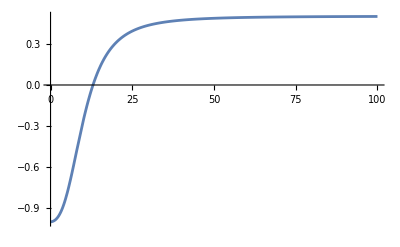

```mathematica
Plot[q[z]/.solq21, {z,0,zinitial}, PlotRange->All]
```

```mathematica
solq21
```

{q→InterpolatingFunction[…]}

```mathematica
dEh/.j->j1/.ϵ->params10a["eps"]/.solq21
```

-Eh[z] (1+InterpolatingFunction[…][z])+(1+z) Eh'[z]==0

```mathematica
solEh21=NDSolve[{dEh/.j->j1/.ϵ->params10a["eps"]/.solq21, Eh[zinitial]==Ehin},Eh,{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10][[1]];
```

```mathematica
Eh[0]/.solEh21
```

630.874

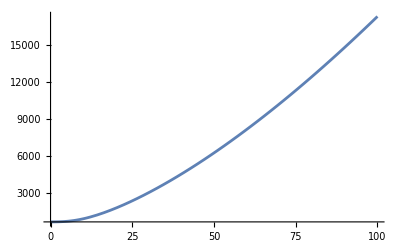

```mathematica
Plot[Eh[z]/.solEh21, {z,0,zinitial}, PlotRange->All]
```